# 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{n,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0}(*{(*maxran-20*)20,limit+.05}*),{(*maxran-25*)(*15*)ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos(*{(*maxran-20*)22,limit+.05}*),Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" },
{{funplot,DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]},{0,1},ControlType->None},
{{ilimpos,If[limpos===Automatic,{22,limit+05},limpos]},ControlType->None},
SaveDefinitions->True,Initialization:>{epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}]}
]
]
```

# 1) Limes superior und limes inferior

a_n=-1/n^2+(-1)^n

lim sup_(n→∞) a_n=?
lim inf_(n→∞) a_n=?

#### Useful formulas

Definition of lim sup and lim inf

(ā)_n:=sup{a_m|m≥n}
(a̲)_n:=inf{a_m|m≥n}

lim sup_(n→∞) a_n=lim_(n→∞) (ā)_n
lim inf_(n→∞) a_n=lim_(n→∞) (a̲)_n

## Plots

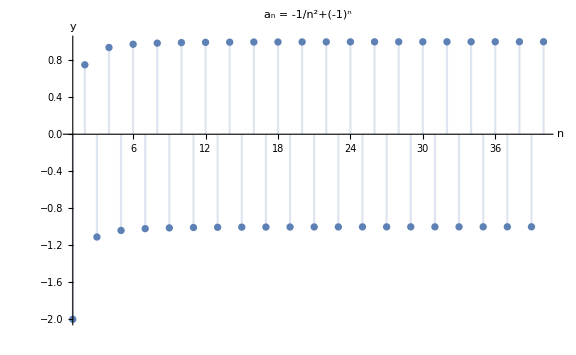

```mathematica
discPlotFun[-1/n^2+(-1)^n,{1,40},{{1,40},All},{},"a_n = -1/n^2+(-1)^n"]
```

## Solution

(ā)_n:=sup{a_m|m≥n}=sup{-1/m^2+(-1)^m|m≥n}=sup{-1/m^2+1|m≥n}=1

(a̲)_n:=inf{a_m|m≥n}=inf{-1/m^2+(-1)^m|m≥n}=inf{-1/m^2-1|m≥n}=-1/n^2-1

lim_(n→∞) (ā)_n=lim_(n→∞) 1=1

lim_(n→∞) (a̲)_n=lim_(n→∞) (-1/n^2-1)=-1

# 2) Häufungspunkte

a_n=(1-n^2+(-1)^n n^3)/(n^3+2)

Häufungspunkte?

## Plots

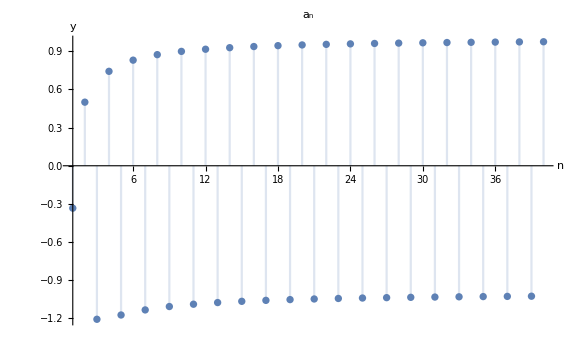

```mathematica
discPlotFun[(1-n^2+(-1)^n n^3)/(n^3+2),{1,40},{{1,40},All},{},"a_n"]
```

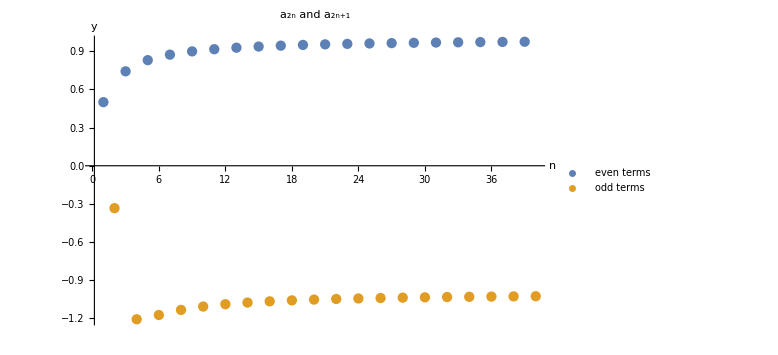

```mathematica
Framed@ListPlot[{Riffle[Table[(1-n^2+n^3)/(n^3+2),{n,2,40,2}],Missing[](*0*)],Prepend[Riffle[Table[(1-n^2-n^3)/(n^3+2),{n,1,40,2}],Missing[](*0*)],Missing[](*0*)]},PlotRange->All,Filling->Axis,ImageSize->Large,AxesLabel->{"n","y"},PlotLabel->Style["a_(2n) and a_(2n+1)",Black,Bold,20],PlotLegends->{"even terms","odd terms"},BaseStyle->{FontSize->20}]
```

## Solution

For large n the sequence behaves as a_n=(1-n^2+(-1)^n n^3)/(n^3+2)≈((-1)^n n^3)/n^3=(-1)^n, which has no limit. But there apparently two repeating elements: +1 and -1. To show that they are Häufungspunkte we have to construct appropriate convergent Teilfolge that have these values as limits:

b_n:=a_(2n)=(1-(2n)^2+(-1)^(2n)(2n)^3)/((2n)^3+2)=(1-(2n)^2+(2n)^3)/((2n)^3+2)

c_n:=a_(2n+1)=(1-(2n+1)^2+(-1)^(2n+1)(2n+1)^3)/((2n+1)^3+2)=(1-(2n+1)^2-(2n+1)^3)/((2n+1)^3+2)

Then:

lim_(n→∞) b_n=lim_(n→∞) (1-(2n)^2+(2n)^3)/((2n)^3+2)=lim_(n→∞) (1/(2n)^3-1/(2n))+1)/(1+2/(2n)^3)=1

lim_(n→∞) c_n=lim_(n→∞) (1-(2n+1)^2-(2n+1)^3)/((2n+1)^3+2)=lim_(n→∞) (1/(2n+1)^3-1/(2n+1)-1)/(1+2/(2n+1)^3)=-1

# 3) Folgen und Grenzwerte

a) a_n=(1-x^(2n))/(2 x^-n+x^(2n)),  x>1

a) b_n=((n+1)(n-1))/(2n+3)

a) c_n=(-2n)/(2 n^2+3n+1)

Konvergent? Grenzwert?

## Solution

## a)

lim_(n→∞) a_n=lim_(n→∞) (1-x^(2n))/(2 x^-n+x^(2n))=lim_(n→∞) (x^(2n)(1/x^(2n)-1))/(x^(2n)(2/x^(3n)+1))=lim_(n→∞) ((1/x^2)^n-1)/(2(1/x^3)^n+1)=-1/1=-1

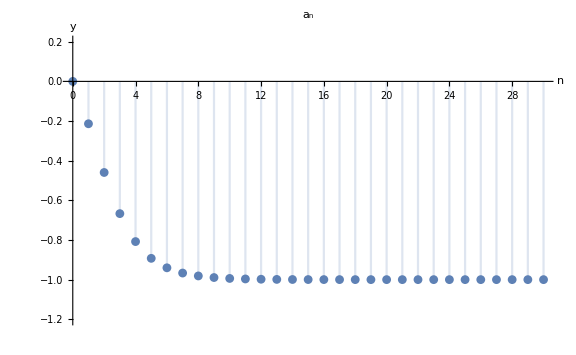

```mathematica
discPlotFun[With[{x=1.3},(1-x^(2n))/(2 x^-n+x^(2n))],{0,30},{-1.2,.2},{},"a_n"]
```

```mathematica
plotLimitDisc[(1-1.3^(2 #))/(2 1.3^-#+1.3^(2 #))&(*(#1^2-#1)/(2 #1^2+3)&*),Ceiling[Log[2+1/#]/Log[1.3](*(1+√(1+12 #-24 #^2))/(4 #)*)]&,{0.00001,1},30,-1,"Sequence a_n, its limit -1 and varying ϵ",False,True,"a_n",{},{22,-.6}]
```

## b)

lim_(n→∞) b_n=lim_(n→∞) ((n+1)(n-1))/(2n+3)=lim_(n→∞) (n^2(1-1/n^2))/(n(2+3/n))=lim_(n→∞) (n(1-1/n^2)/(2+3/n^2))=lim_(n→∞) (n)(lim_(n→∞) (1-1/n^2))/(lim_(n→∞) (2+3/n^2))=(+∞)·1/2=+∞

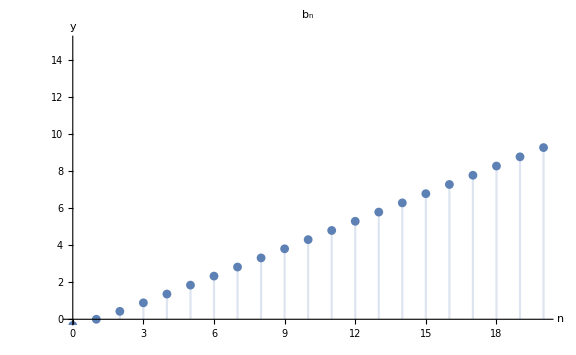

```mathematica
discPlotFun[((n+1)(n-1))/(2n+3),{0,20},{0,15},{},"b_n"]
```

## c)

lim_(n→∞) c_n=lim_(n→∞) (-2n)/(2 n^2+3n+1)=lim_(n→∞) (n(-2))/(n^2(2+3/n+1/n^2))=(-2)lim_(n→∞) (1/n)1/(lim_(n→∞) (2+3/n+1/n^2))=-2 ·0·1/2=0

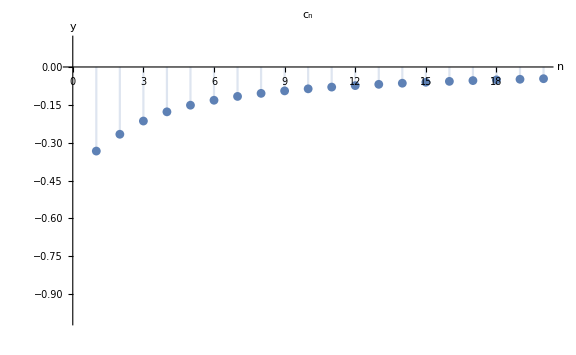

```mathematica
discPlotFun[(-2n)/(2 n^2+3n+1),{1,20},{-1,.1},{},"c_n"]
```

```mathematica
plotLimitDisc[-(2 #1)/(1+3 #1+2 #1^2)&,Ceiling[(2-3 #1)/(4 #1)+1/4 √((4-12 #1+#1^2)/#1^2)]&,{0.00001,.1},100,0,"Sequence c_n, its limit 0 and varying ϵ",True,False,"c_n",{},{70,.1}]
```

# 4) Folgen

∃(a_n) ?, a_n∈ℝ

a) nach oben beschränkt, streng monoton wachsend und divergent

b) nach unten beschränkt, streng monoton wachsend und divergent

c) Cauchy-Folge und uneigentlich gegen +∞ konvergiert

## Solution

## a)

Bounded from above + monotonically increasing → convergent

## b)

E.g. a_n:=n → lim_(n→∞) a_n=+∞

## c)

Cauchy ⇔ convergent in ℝ → limit in ℝ

# 5) Grenzwertarithmetik

Satz 6.5. (2):  Seien (a_n), (b_n) konvergent mit a=lim_(n→∞) a_n und b=lim_(n→∞) b_n. Dann gilt:

lim_(n→∞) (a_n·b_n)=a·b

#### Useful formulas

Add and subtract

a_n b_n-a b=a_n(b_n-b)+(a_n-a)b

Triangle inequality

|x+y|≤ |x|+|y|

## Solution

Let us start with the definition of a limit:

(∀ϵ>0)(∃N∈ℕ)(∀n∈ℕ, n>N)(|a_n b_n-a b|<  ϵ)

We rewrite the expression at hand:

|a_n b_n-a b|=|a_n(b_n-b)+(a_n-a)b|≤ |a_n||b_n-b|+|a_n-a||b|

We also know, that a and b are limits of (a_n) and (b_n), respectively. Thus for each ϵ̄>0 there exist N_a and N_b, such that:

|a_n- a|<  ϵ̄   and |b_n-b|<  ϵ̄

For N_0:=max(N_a,N_b) we therefore get:

|a_n||b_n-b|+|a_n-a||b|≤ |a_n|ϵ̄+ϵ̄|b|

From |a_n- a|<  ϵ̄   it also follows that |a_n|< |a|+ ϵ̄   and so (we already assume that ϵ̄<1 in the following):

|a_n|ϵ̄+ϵ̄|b|≤ (|a|+ϵ̄)ϵ̄+ϵ̄|b|=ϵ̄(|a|+|b|+  ϵ̄)≤ϵ̄ (|a|+|b|+  1)

Putting all things together we arrive at the expression:

|a_n b_n-a b|≤ ϵ̄  (|a|+|b|+  1)

So for each given ϵ>0 (ϵ<1) we can take ϵ̄:=ϵ/(|a|+|b|+  1), from there we find N_0, such that for all n>N_0 it holds that

|a_n b_n-a b|≤ ϵ

as we wanted to show. Note that for ϵ>1 we would get |a_n b_n-a b|≤ ϵ̄  (|a|+|b|+  ϵ̄),  from which we could also extract ϵ̄ analogously to the previous case and obtain desired inequality.

# 6) Rekursion

√(1+√(1+√(1+…)))

a_0=1
a_(n+1)=√(1+a_n),   n≥0

## Plot

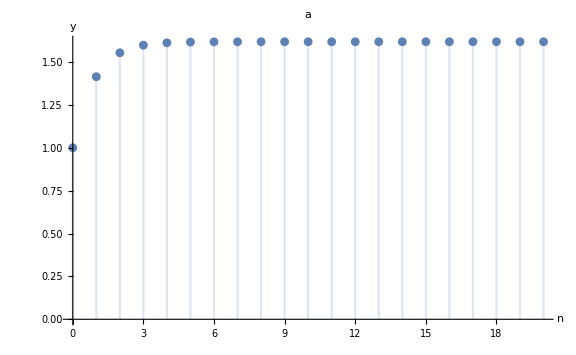

```mathematica
ClearAll[a]
a[0]=1;
a[n_]:=a[n]=√(1+a[n-1])

Framed@DiscretePlot[a[n],{n,0,20},PlotLabel->Style["a",Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]
```

## Solution

## Bounded

First, we show by mathematical induction that a_n<(1+√5)/2:

initial step for n=0:

a_0=1<(1+√5)/2≈1.61803

assume validity for n to prove the same for n+1:

a_(n+1)^2=1+a_n<1+(1+√5)/2=(3+√5)/2=((1+√5)/2)^2 ⇒ a_(n+1)^2<((1+√5)/2)^2⇒ a_(n+1)<(1+√5)/2

## Increasing

Secondly, we show that a_(n+1)>a_n:

a_n<a_(n+1)   ⇔  a_n^2< a_(n+1)^2=1+a_n     and so we want to check that:  a_n^2-a_n-1< 0

Solutions to a_n^2-a_n-1< 0 are (a_n)_(1,2)=(1±√5)/2. From the plot of the function x^2-x-1 and from the property a_n<(1+√5)/2 it is clear that indeed a_n^2-a_n-1< 0 and thus a_(n+1)>a_n.

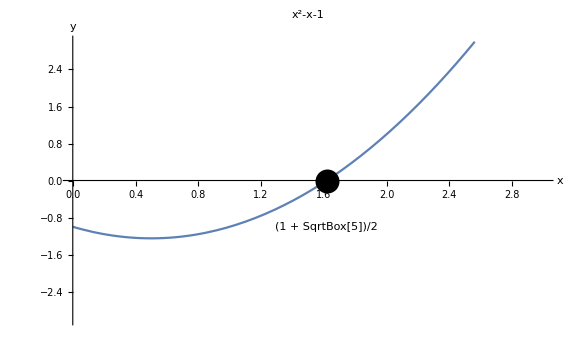

```mathematica
plotFun[x^2-x-1,{{0,3},{-3,3}},{PointSize[.03],Point[{(1+√5)/2,0}],Text["(1 + SqrtBox[5])/2",{(1+√5)/2,-1}]},"x^2-x-1"]
```

## Limit

Sequence a_n is bounded from above and monotonically increasing and therefore has a limit a∈ℝ such that  lim_(n→∞) a_n=a. We can use the claim of exercise Grenzwertarithmetik above, where b_n:=a_n, to show that lim_(n→∞) a_n^2=a^2. By applying the limit to the recursion formula a_(n+1)^2=1+a_n we get:

lim_(n→∞) a_(n+1)^2=lim_(n→∞) (1+a_n)=1+lim_(n→∞) a_n and thus a^2=1+a, which we solved already above with solution a= (1+√5)/2 (value (1-√5)/2 is negative and cannot be the limit as all a_n>0)

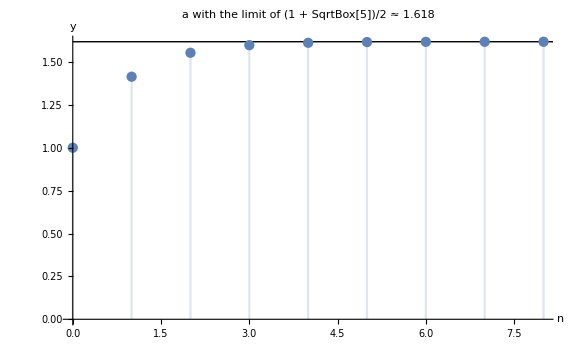

```mathematica
ClearAll[a]
a[0]=1;
a[n_]:=a[n]=√(1+a[n-1])

Framed@DiscretePlot[a[n],{n,0,8},PlotLabel->Style["a with the limit of (1 + SqrtBox[5])/2 ≈ 1.618",Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20},Epilog->{Line[{{0,(1+√5)/2},{10,(1+√5)/2}}]}]
```